```mathematica
SetDirectory[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"out", "schaeferTurek"}]]
```

/home/florian/Projects/university/masters_thesis/code/2D/out/schaeferTurek

```mathematica
srts = Complement[FileNames[], FileNames["*time"], FileNames["cumulant*"]];
cumulants = Complement[FileNames[], FileNames["*time"], FileNames["srt*"]];
getSizes[thelist_]:=Read[StringToStream[#],Number]&/@Flatten[ StringDrop[#,4] &/@StringCases[thelist, RegularExpression["size([0-9]*)"]]] 
sizes = getSizes[srts];
permutations = Ordering[sizes];
sizes = sizes[[permutations]];
cumulants = cumulants[[permutations]];
srts = srts[[permutations]];
```

```mathematica
dragData[input_] := Drop[Map[Delete[#,3]&,input],1000];
liftData[input_] := Drop[Map[Delete[#,2]&,input],1000];

dataFrequency[list_] := Abs[Fourier[ #[[2]]&/@list]];

maximaPositions[list_] :=1+Position[Differences[Sign[Differences[list[[All,2]]]]],-2];
minimaPositions[list_] :=1+Position[Differences[Sign[Differences[list[[All,2]]]]],2]

lastWavelimits[data_]:=Flatten[ Take[maximaPositions[data],-2]];
lastWavelength[data_]:=Differences[lastWavelimits[data]][[1]];

lastWave[data_]  := Take[data,lastWavelimits[data]];

valuesOnly[data_]:=Flatten[Map[Delete[#,1]&,data]];
means[datas_] := Map[Mean[valuesOnly[#]]&,datas];
bothMeansPlotReady[filterFunction_] := {Transpose[{sizes,means[filterFunction /@ Import /@ cumulants]}],Transpose[{sizes,means[filterFunction /@ Import /@ srts]}]};
```

Drop::normal: Nonatomic expression expected at position 1 in Drop[timestep,drag,lift,1000].

General::stop: Further output of Drop::normal will be suppressed during this calculation.

Delete::partw: Part 1 of timestep,drag,lift does not exist.

Delete::partw: Part 1 of 1000 does not exist.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[Delete[timestep,drag,lift,1],Delete[1000,1]].

Delete::partw: Part 1 of timestep,drag,lift does not exist.

General::stop: Further output of Delete::partw will be suppressed during this calculation.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[Delete[timestep,drag,lift,1],Delete[1000,1]].

General::stop: Further output of Drop::seqs will be suppressed during this calculation.

Delete::pkspec: The expression 1. cannot be used as a part specification. Use Key[1.] instead.

General::stop: Further output of Delete::pkspec will be suppressed during this calculation.

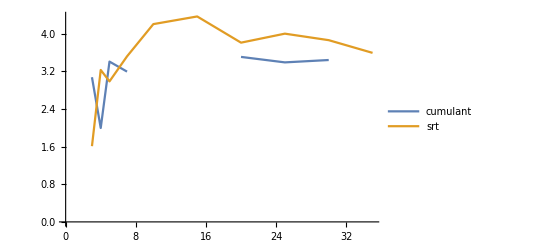

```mathematica
ListLinePlot[bothMeansPlotReady[dragData], PlotLegends->{"cumulant","srt"}]
```

```mathematica
getLastWaveLift["cumulant",15]
getLastWavelengthLift["cumulant",15]
```

getLastWaveLift[cumulant,15]

getLastWavelengthLift[cumulant,15]

```mathematica
plotCumulantsFromTo[4,9]
```

plotCumulantsFromTo[4,9]

```mathematica
plotSRTFromTo[10,10]
```

plotSRTFromTo[10,10]

```mathematica
plotCumulantsFrequencyFromToClip[2,8,3]
plotSRTFrequencyFromToClip[2,8,3]
```

plotCumulantsFrequencyFromToClip[2,8,3]

plotSRTFrequencyFromToClip[2,8,3]

```mathematica
points = getLiftData["cumulant", 10];

maxima=1+Position[Differences[Sign[Differences[points[[All,2]]]]],-2]
minima=1+Position[Differences[Sign[Differences[points[[All,2]]]]],2]

peaks=Extract[points,maxima]
ListLinePlot[points,Prolog->{PointSize[Large],Red,Point[Extract[points,maxima]],Green,Point[Extract[points,minima]]}]
```

Part::partd: Part specification getLiftData[cumulant,10]⟦All,2⟧ is longer than depth of object.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[getLiftData[cumulant,10]⟦All,2⟧].

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[Sign[Differences[getLiftData[cumulant,10]⟦All,2⟧]]].

{}

Part::partd: Part specification getLiftData[cumulant,10]⟦All,2⟧ is longer than depth of object.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[getLiftData[cumulant,10]⟦All,2⟧].

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[Sign[Differences[getLiftData[cumulant,10]⟦All,2⟧]]].

{{2,2,2,4}}

{}

Extract::partd: Part specification {2,2,2,4} is longer than depth of object.

ListLinePlot::lpn: getLiftData[cumulant,10.] is not a list of numbers or pairs of numbers.

ListLinePlot[getLiftData[cumulant,10],Prolog→{PointSize[Large],RGBColor[1, 0, 0],Point[{}],RGBColor[0, 1, 0],Point[Extract[getLiftData[cumulant,10],{{2,2,2,4}}]]}]

```mathematica
getWavelengthLift[]
```

getWavelengthLift[]